```mathematica
UNIVERSITY COLLEGE DUBLIN
```

```mathematica
School of Mathematics and Statistics
```

# DATA and COMPUTATION SCIENCE

```mathematica
___________________________________________________________________________________________________
```

```mathematica
Module Name: Mathematica For Research \[MathematicaIcon]
Subject: Applied& Computational Maths
Module Code: ACM40730
Trimester: Autumn
Module Coordinator:Dr Niels Warburton
Student Name: Utpal Mishra
Student Number: 20207425
___________________________________________________________________________________________________
```

```mathematica
FINAL PROJECT
```

## Project Objective

The general objective of the project is to design a system and automated the process of breast cancer detection using the techniques of machine learning and provide some assistance in diagnosis and treatment to the radiologists and physicians. In order to achieve this, the following are some specific objectives : 

1. To analyse previous related works on breast cancer detection and classification so as to select relevant methods and techniques.
2. To opt for befitting methods for segmentation, data preprocessing, feature extraction and classification.
3. To deliver a prototype for the proposed approach.
4. To assess the performance of the project in terms of f-score, precision, recall, error and classification accuracy.
5. To deploy a time - efficient and reliable prototype that could assist pathologists.

## Abstract

Among all the form of cancer in women, breast cancer contributes to over 20 % and has resulted with more in millions new cases each year (over 5 lakh recorded in 2012). With lack in diagnosis and treatment in India, a women is detected with breast cancer in every 4 minutes along-with the highest death cases world wide (2012) i.e. in every 8 minutes. Automating the process will be really beneficial for the people suffering from cancer, being can be cost - effective with elevated accuracy. In this project, KNN and SVM are found to be the most useful algorithms to work with then the data undertaken.

## Introduction

Breast cancer is the fifth most common cause of death and the second most common type of cancer after lung cancer. The National Breast Cancer Foundation has valued around 2 lakh fresh cases of breast cancer and annually, witnessing 40, 000 deaths in women while in men, these numbers are 1700 and 450, correspondingly.

Cancer comes under a class of diseases which are characterised by abnormal growth of cells which hinder surrounding healthy cell in the body. Breast cancer starts to penetrates in the breast cells of both men and women and spread to different body parts. It results in lump formation near the cells due accumulation of tissues thus, early detection is crucial. Recent statistics show that breast cancer is a serious disease with a high incidence rate and one of the leading causes of the early death of women. Being a paramount stage, statistics show a five - year survival rate of 96 % in early diagnosis of breast cancer as being one of the curable form of cancer. At the early stage, detection can be performed using the following two strategies:

A. Early Diagnosis: Using effective treatments to reduce the risk of cancer by escalating the identification proportion at the early stage.
  
B. Screening: Rectifying the presence of cancerous cells before the symptoms can showcase using various tools such as: 
i. Breast Self - Exam (BSE)
ii. Clinical Breast Exam (CBE)
iii. Mammography

*This research project aims to probe into the possibility of detecting and classifying breast cancer from the Breast Cancer Wisconsin (Diagnostic) Data.

## Algorithms

Following are the machine learning classification algorithms used for detecting breast cancer:

#### 1. Naive Bayes (NB)

Naive Bayes is a probabilistic classifier which applies Bayes' theorem with strong independent assumptions. In this model, all properties are separately taken into consideration to find any relationship between them. It assumes that predictive attributes are conditionally independent given the class. Additionally, the values of the numeric attributes are distributed within each class. Naive Bayes is fast and performs well even with a small dataset. However, it is hard to find independent properties in real life. Researchers have deployed NB classifiers for breast cancer detection and achieved the maximum accuracy with only five dominant.

#### 2. Decision Tree (DT)

Decision Tree is a data mining technique used for early detection of breast cancer. It is a model that presents classification or regression as a tree. In this model, the dataset is split into small sub - data, then into smaller ones. As a result, the tree is developed and at the last level reveals the result. In a tree structure, the leaves characterise the class labels while the branches characterise conjunctions of features which lead to the class labels. Hence, DT is not sensitive to noise. Now, if we are dealing with a larger dataset, greater are the splits and such huge trees result in elevating the complexity and leads to overfitting. A simple approach to limit the splitting is by fixing the minimum training dataset at the input and the maximum depth of the decision making tree. Another approach is by using the method of Pruning.
   
An effective technique to optimize the performance of Decision Tree is by simply getting rid of the attributes with lesser information or higher entropy. There are two approaches to execute this technique to either start from root or leaves. The bottom - up method in which child attributes having lesser significance are removed without altering the accuracy is known as Reduce Error Pruning.

#### 3. Random Forest (RF)

This algorithm is an extension of Decision Tree, as being the building block.The name "Random Forest", is self - explanatory where "Forest" signifies averaging the prediction of the tree and "Random" explains two concepts : i.For tree building : random sampling of training data points for building the tree.ii.For splitting nodes : after sample data is fetched, a random subset of features is chosen for analysis to split the nodes, as the tree learns from the random sample and their features.For building a tree, multiple samples are used multiple times which is known as Bootstrapping.
  
  It can also be defined as a random sampling of observational data with replacement.While training each tree, different samples used for building trees might have a higher variance but the cumulative variance of the forest must be low and not at the cost of an increase in bias.The prediction is made by averaging the prediction of each Decision Tree and is termed as Bootstrap Aggregating or Bagging.It can also be said as a different randomized (bootstrapped) subset of data for making up the individual trees that are trained and then averaged for prediction.The contrast between Decision Tree and Random Forest is that, instead of shortlisting the result from a single tree, multiple trees are taken into consideration and evaluated for prediction.As in epitome, predicting a product in the market by the cumulative reviews for E - commerce websites, Google and Youtube.

#### 4. K - Nearest Neighbors (KNN)

KNN is a supervised learning method. It can be used for diagnosing and classifying cancer. In this method, the model is trained in a specific field and new data is given to it. Furthermore, similar data is used by the machine for detecting "K". Therefore, the machine finds KNN for the unknown data. It is recommended to choose a large dataset for training also K value must be an odd number determining closeness. 

For calculating the closeness, the distance between data observations is estimated and is known as Minkowski Distance. The distance calculated in a normed vector space i.e. space where the distance is observed in vectors is called a Minkowski Distance. "Normed '' signifies that vectors have length and no vector can have negative length.

#### 5. Support Vector Machines (SVM)

SVM is a supervised machine learning algorithm that is a pattern classification model. It is used as a training algorithm for learning classification and regression rules from collected data. The motive of this method is to segregate data until a hyperplane with high minimum distance is found. Using SVM, we can classify two or more data types. SVM is an efficient method for diagnosing breast cancer. Its accuracy can increase when combined with feature selection. This accuracy can be obtained on the WBCD dataset, considering five features.SVM is the most efficient way of statistical learning. It can easily identify the decision boundaries between different classes of breast cancer. The input features are selected after calculating the F - score of each input feature. The significance of each feature is evaluated by it' s F - score. The SVM parameters are optimised by grid search.
   
   It is called a Discriminative Classifier and learns about classification from given statistics depending on the observed data.It can also be called as a Discriminative Model or a Conditional Model for statistical classification in (Supervised) Machine Learning defined by separating hyperplanes.In a multi - dimensional space for separating classes, labeled training data are used to form optimal hyperplanes (2 D) while 3 D hyperplanes are used for kernel transformations.

#### 6. Neural Networks (NN)

ANN is a machine learning model similar to the human brain' s nerve system having a large number of interconnected nodes. Each node has two states : 0 represents the inactive state and 1 represents the active state. Furthermore, each node has either a positive or a negative weight that tunes the strength of that node and can activate or deactivate it. The machine is trained on samples of data using ANN. The trained machine is then used to detect the pattern of hidden data. It can search for patterns between patients' healthcare and personal records to identify high - risk lesions.

The advantages of using ANN are - They can learn and model non - linear and complex relationships. They can generalise. No restrictions are imposed on the input variables (like how they should be distributed).Its region growing - based segmentation method is improved by using the extracted intensity features from ROIs and applying the ANN to generate an adaptive threshold.

## Loading the Datasets

## About data

1. The Breast Cancer Classification data has been extracted from Wisconsin Dataset. 
2. The data contain “diagnosis” as the dependent variable and rest 31 numerical features as independent ones. 
3. Within the attribute “diagnosis”, category 1 represents “Malignant” (Abnormal) while 0 reflects “Benign” (Normal).
4. The dimensions of the data are 567x32 which has been divided into training (0.80) and testing data (0.20) with shapes {455, 32} and {112, 32}, respectively.

## Loading the training data

```mathematica
Clear[train, test]
```

```mathematica
train=Import["E:\\UCD\\Lectures\\Semester 1\\Mathematica\\PROJECT\\train.csv"];
header=train[[1]];
traindata=train[[2;;]];
train=Thread[header->#]&/@traindata//Map[Association]//Dataset;
Dimensions[train]
train[1;;5]
```

{455,32}

## Loading the testing data

```mathematica
test=Import["E:\\UCD\\Lectures\\Semester 1\\Mathematica\\PROJECT\\test.csv"];
header=test[[1]];
testdata=test[[2;;]];
test=Thread[header->#]&/@testdata//Map[Association]//Dataset;
Dimensions[test]
test[1;;5]
```

{114,32}

## Preparing the Model

## Anomalies Detection

### Anomalies are also referred to as outliers, noise, deviations and exceptions. Anomaly Detection is a data mining technique to remove the data points that does not fit the model well. In data analysis, rectification of an abnormal behaving data point which is significantly different from its relative values is also termed as Anomaly Detection. One of the prominent density based technique used is K-Nearest Nearest, and the same is reflected through the obtained fitted model evaluations compared to other models.

```mathematica
adtrain = AnomalyDetection[train]
trainoutliers = FindAnomalies[adtrain, train]
```

AnomalyDetectorFunction[…]

```mathematica
adtest = AnomalyDetection[test]
testoutliers  = FindAnomalies[adtest, test]
```

AnomalyDetectorFunction[…]

## Preparing Y_train and Y_test columns for the model

```mathematica
trainPrep  = train[All, "diagnosis"];
testPrep = test[All, "diagnosis"];
```

## Extracting the features for training and testing data

```mathematica
trainFeatures = train[1;;Length[train],{"radius_mean", "texture_mean", "perimeter_mean", "area_mean", "smoothness_mean", "compactness_mean", "concavity_mean", "concave points_mean", "symmetry_mean", "fractal_dimension_mean", "radius_se", "texture_se", "perimeter_se", "area_se", "smoothness_se", "compactness_se", "concavity_se", "concave points_se", "symmetry_se", "fractal_dimension_se", "radius_worst", "texture_worst", "perimeter_worst", "area_worst", "smoothness_worst", "compactness_worst", "concavity_worst", "concave points_worst", "symmetry_worst", "fractal_dimension_worst", "diagnosis"}];

testFeatures = test[1;;Length[test],{"radius_mean", "texture_mean", "perimeter_mean", "area_mean", "smoothness_mean", "compactness_mean", "concavity_mean", "concave points_mean", "symmetry_mean", "fractal_dimension_mean", "radius_se", "texture_se", "perimeter_se", "area_se", "smoothness_se", "compactness_se", "concavity_se", "concave points_se", "symmetry_se", "fractal_dimension_se", "radius_worst", "texture_worst", "perimeter_worst", "area_worst", "smoothness_worst", "compactness_worst", "concavity_worst", "concave points_worst", "symmetry_worst", "fractal_dimension_worst", "diagnosis"}];
```

## Flattening the training and testing data

```mathematica
trainFinal=Flatten[Normal@trainFeatures[1;;Length[trainPrep],{Most@#->Last@#}&],1];
testFinal=Flatten[Normal@testFeatures[1;;Length[testPrep],{Most@#->Last@#}&],1];
```

## Data Visualization

## Frequency Plot of Diagnosis into Malignant and Benign

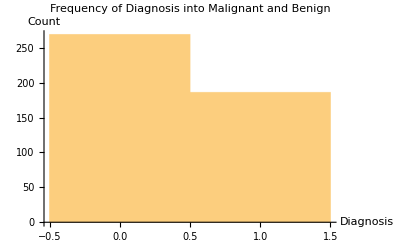

```mathematica
Histogram[train[All, 32], AxesLabel->{HoldForm[Diagnosis],HoldForm[Count]},PlotLabel->HoldForm[Frequency of Diagnosis into Malignant and Benign],LabelStyle->{GrayLevel[0],Bold}]
```

## Features Histogram

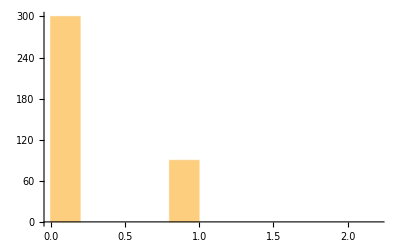
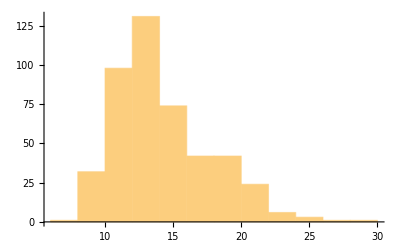
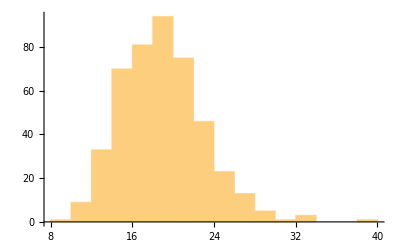
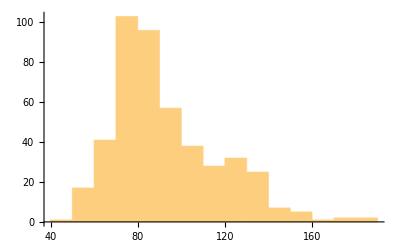
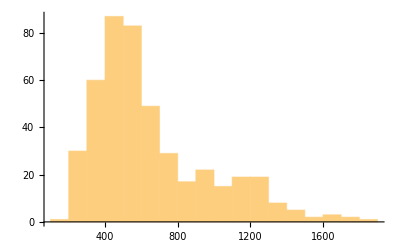
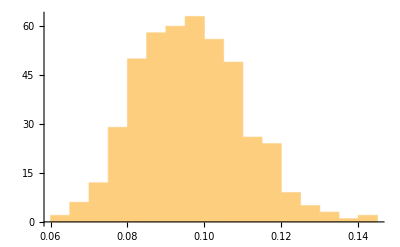
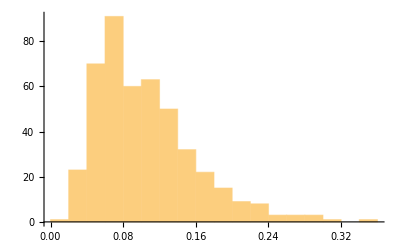
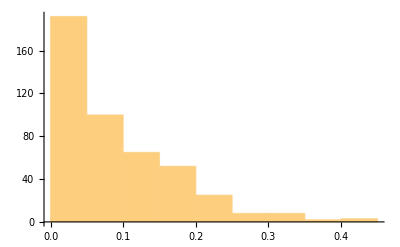

```mathematica
Table[Histogram[train[All, i]], {i, 31}]
```

## Building Classification Model

## Explicit Model Functions

### Classification Function

```mathematica
Classification[data_, method_] := Classify[data,Method->method]
```

### Algorithm Information

```mathematica
AlgorithmInformation[model_, about_] := ClassifierInformation[model,about]
```

### Model Information

```mathematica
ModelInformation[model_] := Information[model]
Info[mod_]:=Module[{ModelInformation}, ModelInformation[mod]; mod]
(* Info[mod_]:=Block[{ModelInformation}, ModelInformation[mod]; mod] *)
```

## Naive Bayes Classification Algorithm

### Fitting the model

```mathematica
Set[algoNB, Classify[trainFinal, Method -> "NaiveBayes", TrainingProgressReporting->"SimplePanel"]]
```

ClassifierFunction[…]

### About the algorithm

```mathematica
ClassifierInformation[algoNB,"MethodDescription"]
```

The naive Bayes classifier assumes that features are generated independently given the class and uses Bayes' theorem to predict the class.

### Evaluation Measurements

PROPERTIES: {Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionDistribution,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeNumber,FalseNegativeRate,FalsePositiveExamples,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictiveValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TrueNegativeNumber,TruePositiveExamples,TruePositiveNumber,WorstClassifiedExamples}

```mathematica
cmNB=ClassifierMeasurements[algoNB,testFinal]
```

ClassifierMeasurementsObject[…]

```mathematica
(* cmNB/@{"Accuracy","Error", "FScore",  "Precision", "Recall", "AreaUnderROCCurve"}//TableForm *)
```

```mathematica
PROPERTIES = {"Accuracy","EvaluationTime", "Error", "FScore",  "Precision", "Recall", "Specificity", "AreaUnderROCCurve"};
For[i =1, i≤ Length[PROPERTIES], i++, Print[PROPERTIES[[i]], ": " ,cmNB[PROPERTIES[[i]]]]]
```

Accuracy: 0.929825

EvaluationTime: 0.007

Error: 0.0701754

FScore: <|0→0.953488,1→0.857143|>

Precision: <|0→0.97619,1→0.8|>

Recall: <|0→0.931818,1→0.923077|>

Specificity: <|0→0.923077,1→0.931818|>

AreaUnderROCCurve: <|0→0.994318,1→0.994318|>

### Confusion Matrix Plot and Accuracy vs Rejection Rate Plot

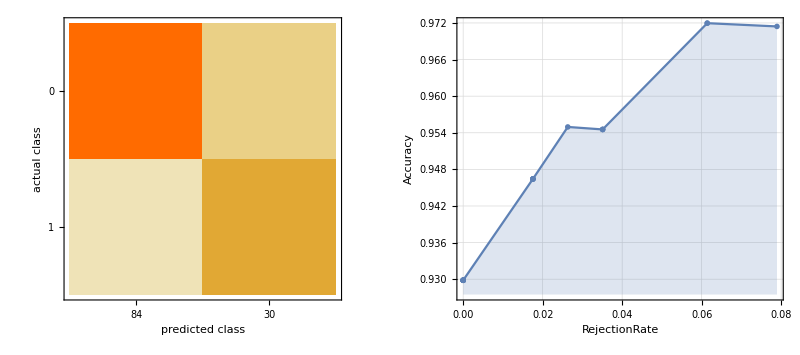

```mathematica
GraphicsRow[{cmNB["ConfusionMatrixPlot"],cmNB["AccuracyRejectionPlot"]}, Background->Black]
```

### Model Evaluations

```mathematica
Map[Info, algoNB]
```

ClassifierFunction[…]

```mathematica
ModelInformation /@ {algoNB}
```

{Classifier information
Data type | Mixed (number: 30)
Classes | ,,01
Accuracy | (94.01.6) %
Method | NaiveBayes
Single evaluation time | 5.09 ms/example
Batch evaluation speed | 7.69 examples/ms
Loss | 0.699 ± 0.29
Model memory | 361. kB
Training examples used | 455 examples
Training time | 488. ms
 | }

## Decision Tree Classification Algorithm

### Fitting the model

```mathematica
Set[algoDT, Classify[trainFinal, Method->"DecisionTree"]]
```

ClassifierFunction[…]

### About the algorithm

```mathematica
ClassifierInformation[algoDT,"MethodDescription"]
```

The decision tree classifier models class probabilities with a decision tree constructed using the CART algorithm.

### Evaluation Measurements

PROPERTIES : 
{Accuracy, AccuracyBaseline, AccuracyRejectionPlot, AreaUnderROCCurve, BatchEvaluationTime, BestClassifiedExamples, ClassifierFunction, ClassMeanCrossEntropy, ClassRejectionRate, CohenKappa, ConfusionDistribution, ConfusionFunction, ConfusionMatrix, ConfusionMatrixPlot, CorrectlyClassifiedExamples, DecisionUtilities, Error, EvaluationTime, Examples, F1Score, FalseDiscoveryRate, FalseNegativeExamples, FalseNegativeNumber, FalseNegativeRate, FalsePositiveExamples, FalsePositiveNumber, FalsePositiveRate, GeometricMeanProbability, IndeterminateExamples, LeastCertainExamples, Likelihood, LogLikelihood, MatthewsCorrelationCoefficient, MeanCrossEntropy, MeanDecisionUtility, MisclassifiedExamples, MostCertainExamples, NegativePredictiveValue, Perplexity, Precision, Probabilities, ProbabilityHistogram, Properties, Recall, RejectionRate, Report, ROCCurve, ScottPi, Specificity, TopConfusions, TrueNegativeExamples, TrueNegativeNumber, TruePositiveExamples, TruePositiveNumber, WorstClassifiedExamples}

```mathematica
cmDT=ClassifierMeasurements[algoDT,testFinal]
```

ClassifierMeasurementsObject[…]

```mathematica
(* cmDT/@{"Accuracy","FScore","Error",  "Precision", "Recall"}//TableForm *)
```

```mathematica
PROPERTIES = {"Accuracy","EvaluationTime", "Error", "FScore",  "Precision", "Recall", "Specificity", "AreaUnderROCCurve"};
i=1; While[i≤ Length[PROPERTIES],Print[PROPERTIES[[i]], ": " ,cmDT[PROPERTIES[[i]]]]; i++]
```

Accuracy: 0.868421

EvaluationTime: 0.0032

Error: 0.131579

FScore: <|0→0.909091,1→0.761905|>

Precision: <|0→0.974026,1→0.648649|>

Recall: <|0→0.852273,1→0.923077|>

Specificity: <|0→0.923077,1→0.852273|>

AreaUnderROCCurve: <|0→0.965472,1→0.971154|>

### Confusion Matrix Plot and ROC Curve

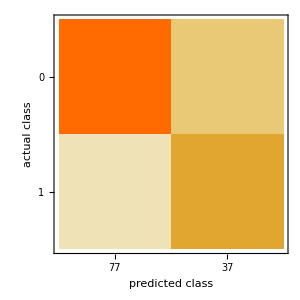

```mathematica
GraphicsRow[{cmDT["ConfusionMatrixPlot"]}, Background->LightYellow]
```

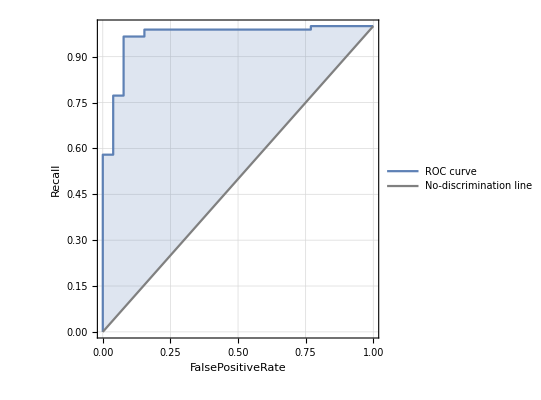
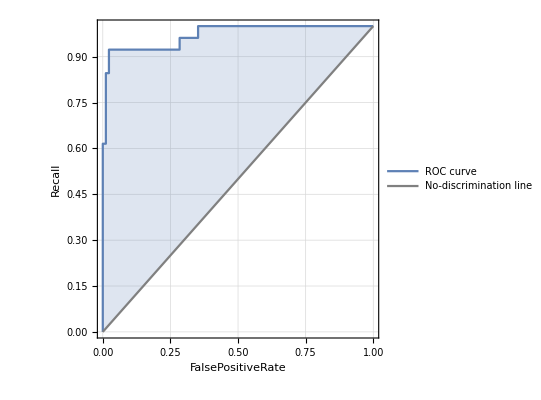
<|0→-Graphics-,1→-Graphics-|>

```mathematica
cmDT["ROCCurve"]
```

### Model Evaluations

```mathematica
Info[algoDT]
```

ClassifierFunction[…]

```mathematica
ModelInformation[algoDT]
```

Classifier information
Data type | Mixed (number: 30)
Classes | ,,01
Accuracy | (91.13.2) %
Method | DecisionTree
Single evaluation time | 2.54 ms/example
Batch evaluation speed | 43.8 examples/ms
Loss | 0.284 ± 0.13
Model memory | 210. kB
Training examples used | 455 examples
Training time | 842. ms
 |

## Random Forest Classification Algorithm

### Fitting the model

```mathematica
Set[algoRF, Classify[trainFinal, Method->"RandomForest"]]
```

ClassifierFunction[…]

### About the algorithm

```mathematica
ClassifierInformation[algoRF,"MethodDescription"]
```

The random forest classifier uses an ensemble of decision trees to predict the class. Each decision tree has been trained on a random subset of the training set, and only uses a random subset of the features.

### Evaluation Measurements

PROPERTIES : 
 {Accuracy, AccuracyBaseline, AccuracyRejectionPlot, AreaUnderROCCurve, BatchEvaluationTime, BestClassifiedExamples, ClassifierFunction, ClassMeanCrossEntropy, ClassRejectionRate, CohenKappa, ConfusionDistribution, ConfusionFunction, ConfusionMatrix, ConfusionMatrixPlot, CorrectlyClassifiedExamples, DecisionUtilities, Error, EvaluationTime, Examples, F1Score, FalseDiscoveryRate, FalseNegativeExamples, FalseNegativeNumber, FalseNegativeRate, FalsePositiveExamples, FalsePositiveNumber, FalsePositiveRate, GeometricMeanProbability, IndeterminateExamples, LeastCertainExamples, Likelihood, LogLikelihood, MatthewsCorrelationCoefficient, MeanCrossEntropy, MeanDecisionUtility, MisclassifiedExamples, MostCertainExamples, NegativePredictiveValue, Perplexity, Precision, Probabilities, ProbabilityHistogram, Properties, Recall, RejectionRate, Report, ROCCurve, ScottPi, Specificity, TopConfusions, TrueNegativeExamples, TrueNegativeNumber, TruePositiveExamples, TruePositiveNumber, WorstClassifiedExamples}

```mathematica
cmRF=ClassifierMeasurements[algoRF,testFinal]
```

ClassifierMeasurementsObject[…]

```mathematica
(* cmRF/@{"Accuracy","FScore","Error",  "Precision"}//TableForm *)
```

```mathematica
PROPERTIES = {"Accuracy","EvaluationTime", "Error", "FScore",  "Precision", "Recall", "Specificity", "AreaUnderROCCurve"};
For[i =1, i≤ Length[PROPERTIES], i++, Print[PROPERTIES[[i]], ": " ,cmRF[PROPERTIES[[i]]]]]
```

Accuracy: 0.964912

EvaluationTime: 0.00619

Error: 0.0350877

FScore: <|0→0.976744,1→0.928571|>

Precision: <|0→1.,1→0.866667|>

Recall: <|0→0.954545,1→1.|>

Specificity: <|0→1.,1→0.954545|>

AreaUnderROCCurve: <|0→0.998252,1→0.997815|>

### Confusion Matrix Plot and Confusion Distribution

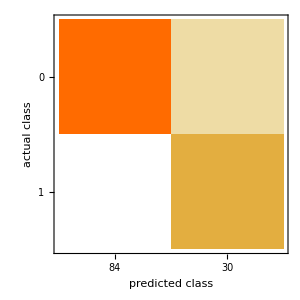

```mathematica
GraphicsRow[{cmRF["ConfusionMatrixPlot"],cmRF["ConfusionDistribution"]}, Background->Orange]
```

### Model Evaluations

```mathematica
Info/@algoRF
```

ClassifierFunction[…]

```mathematica
Map[ModelInformation, {algoRF}]
```

{Classifier information
Data type | Mixed (number: 30)
Classes | ,,01
Accuracy | (93.71.6) %
Method | RandomForest
Single evaluation time | 4.79 ms/example
Batch evaluation speed | 20.8 examples/ms
Loss | 0.198 ± 0.017
Model memory | 309. kB
Training examples used | 455 examples
Training time | 4.98 s
 | }

## Logistic Regression Classification Algorithm

### Fitting the model

```mathematica
Set[algoLR, Classify[trainFinal, Method->"LogisticRegression"]]
```

ClassifierFunction[…]

### About the algorithm

```mathematica
ClassifierInformation[algoLR,"MethodDescription"]
```

The logistic regression classifier models class probabilities with logistic functions of linear combinations of features. It is also called log-linear model, softmax regression, or maximum-entropy classifier.

### Evaluation Measurements

PROPERTIES : 
{Accuracy, AccuracyBaseline, AccuracyRejectionPlot, AreaUnderROCCurve, BatchEvaluationTime, BestClassifiedExamples, ClassifierFunction, ClassMeanCrossEntropy, ClassRejectionRate, CohenKappa, ConfusionDistribution, ConfusionFunction, ConfusionMatrix, ConfusionMatrixPlot, CorrectlyClassifiedExamples, DecisionUtilities, Error, EvaluationTime, Examples, F1Score, FalseDiscoveryRate, FalseNegativeExamples, FalseNegativeNumber, FalseNegativeRate, FalsePositiveExamples, FalsePositiveNumber, FalsePositiveRate, GeometricMeanProbability, IndeterminateExamples, LeastCertainExamples, Likelihood, LogLikelihood, MatthewsCorrelationCoefficient, MeanCrossEntropy, MeanDecisionUtility, MisclassifiedExamples, MostCertainExamples, NegativePredictiveValue, Perplexity, Precision, Probabilities, ProbabilityHistogram, Properties, Recall, RejectionRate, Report, ROCCurve, ScottPi, Specificity, TopConfusions, TrueNegativeExamples, TrueNegativeNumber, TruePositiveExamples, TruePositiveNumber, WorstClassifiedExamples}

```mathematica
cmLR=ClassifierMeasurements[algoLR,testFinal]
```

ClassifierMeasurementsObject[…]

```mathematica
(* cmLR/@{"Accuracy","FScore","Error",  "Precision"}//TableForm *)
```

```mathematica
PROPERTIES = {"Accuracy","EvaluationTime", "Error", "FScore",  "Precision", "Recall", "Specificity", "AreaUnderROCCurve"};
i=1; While[i≤ Length[PROPERTIES],Print[PROPERTIES[[i]], ": " ,cmLR[PROPERTIES[[i]]]]; i++]
```

Accuracy: 0.947368

EvaluationTime: 0.003

Error: 0.0526316

FScore: <|0→0.965909,1→0.884615|>

Precision: <|0→0.965909,1→0.884615|>

Recall: <|0→0.965909,1→0.884615|>

Specificity: <|0→0.884615,1→0.965909|>

AreaUnderROCCurve: <|0→0.982517,1→0.982517|>

### Confusion Matrix Plot and Probability Histogram

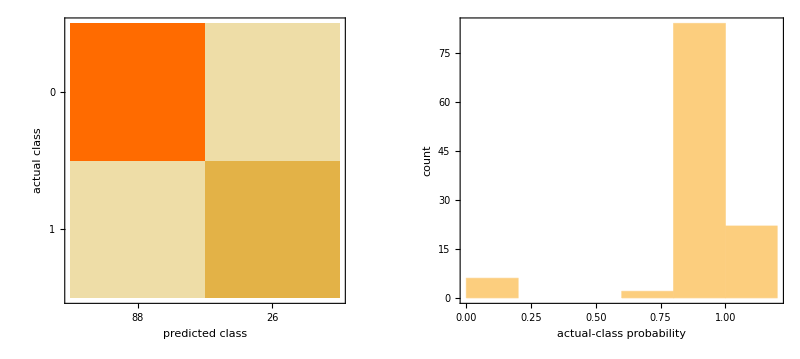

```mathematica
GraphicsRow[{cmLR["ConfusionMatrixPlot"], cmLR["ProbabilityHistogram"]}, Background->LightGreen]
```

### Model Evaluations

```mathematica
Info[algoLR]
```

ClassifierFunction[…]

```mathematica
Map[ModelInformation[#]&,{algoLR}]
```

{Classifier information
Data type | Mixed (number: 30)
Classes | ,,01
Accuracy | (96.51.4) %
Method | LogisticRegression
Single evaluation time | 2.54 ms/example
Batch evaluation speed | 53.7 examples/ms
Loss | 0.0655 ± 0.038
Model memory | 272. kB
Training examples used | 455 examples
Training time | 1.72 s
 | }

## Nearest Neighbors Classification Algorithm

### Fitting the model

```mathematica
Set[algoKNN, Classify[trainFinal, Method->"NearestNeighbors"]]
```

ClassifierFunction[…]

### About the algorithm

```mathematica
ClassifierInformation[algoKNN,"MethodDescription"]
```

The nearest neighbors classifier infers the class of a new example by analyzing its nearest neighbors in the feature space. In its simplest form, it picks the commonest class amongst the "k"-nearest neighbors.

### Evaluation Measurements

PROPERTIES : 
{Accuracy, AccuracyBaseline, AccuracyRejectionPlot, AreaUnderROCCurve, BatchEvaluationTime, BestClassifiedExamples, ClassifierFunction, ClassMeanCrossEntropy, ClassRejectionRate, CohenKappa, ConfusionDistribution, ConfusionFunction, ConfusionMatrix, ConfusionMatrixPlot, CorrectlyClassifiedExamples, DecisionUtilities, Error, EvaluationTime, Examples, F1Score, FalseDiscoveryRate, FalseNegativeExamples, FalseNegativeNumber, FalseNegativeRate, FalsePositiveExamples, FalsePositiveNumber, FalsePositiveRate, GeometricMeanProbability, IndeterminateExamples, LeastCertainExamples, Likelihood, LogLikelihood, MatthewsCorrelationCoefficient, MeanCrossEntropy, MeanDecisionUtility, MisclassifiedExamples, MostCertainExamples, NegativePredictiveValue, Perplexity, Precision, Probabilities, ProbabilityHistogram, Properties, Recall, RejectionRate, Report, ROCCurve, ScottPi, Specificity, TopConfusions, TrueNegativeExamples, TrueNegativeNumber, TruePositiveExamples, TruePositiveNumber, WorstClassifiedExamples}

```mathematica
cmKNN=ClassifierMeasurements[algoKNN,testFinal]
```

ClassifierMeasurementsObject[…]

```mathematica
(* cmKNN/@{"Accuracy","FScore","Error",  "Precision"}//TableForm *)
```

```mathematica
PROPERTIES = {"Accuracy","EvaluationTime", "Error", "FScore",  "Precision", "Recall", "Specificity", "AreaUnderROCCurve"};
For[i =1, i≤ Length[PROPERTIES], i++, Print[PROPERTIES[[i]], ": " ,cmKNN[PROPERTIES[[i]]]]]
```

Accuracy: 0.991228

EvaluationTime: 0.0034

Error: 0.00877193

FScore: <|0→0.99435,1→0.980392|>

Precision: <|0→0.988764,1→1.|>

Recall: <|0→1.,1→0.961538|>

Specificity: <|0→0.961538,1→1.|>

AreaUnderROCCurve: <|0→0.997815,1→0.997815|>

### Confusion Matrix Plot and Accuracy vs Rejection Plot

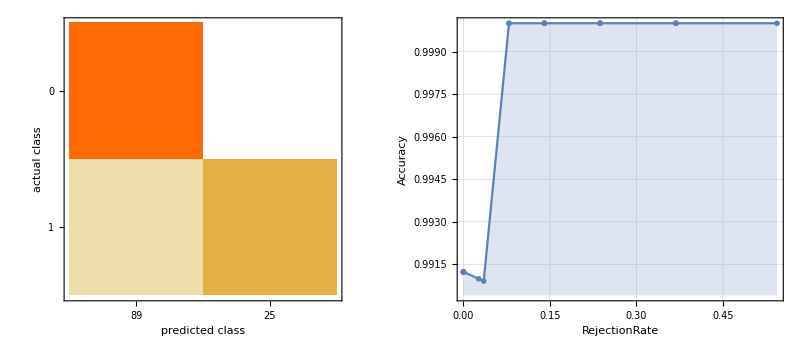

```mathematica
GraphicsRow[{cmKNN["ConfusionMatrixPlot"],cmKNN["AccuracyRejectionPlot"]}, Background->LightGray]
```

### Model Evaluations

```mathematica
Info[algoKNN]
```

ClassifierFunction[…]

```mathematica
Map[ModelInformation ,{algoKNN}]
```

{Classifier information
Data type | Mixed (number: 30)
Classes | ,,01
Accuracy | (96.21.9) %
Method | NearestNeighbors
Single evaluation time | 2.65 ms/example
Batch evaluation speed | 37.1 examples/ms
Loss | 0.168 ± 0.038
Model memory | 324. kB
Training examples used | 455 examples
Training time | 722. ms
 | }

## Support Vector Machine Classification Algorithm

### Fitting the model

```mathematica
Set[algoSVM, Classify[trainFinal,Method->"SupportVectorMachine"]]
```

ClassifierFunction[…]

### About the algorithm

```mathematica
ClassifierInformation[algoSVM,"MethodDescription"]
```

The support vector machine classifier separates the training data into two classes using a 
			maximum-margin hyperplane. The original feature space can be mapped into a higher dimensional space to 
			improve linear separability. The multi-class classification problem is reduced to a set of binary 
			classification problems.

### Evaluation Measurements

PROPERTIES : 
{Accuracy, AccuracyBaseline, AccuracyRejectionPlot, AreaUnderROCCurve, BatchEvaluationTime, BestClassifiedExamples, ClassifierFunction, ClassMeanCrossEntropy, ClassRejectionRate, CohenKappa, ConfusionDistribution, ConfusionFunction, ConfusionMatrix, ConfusionMatrixPlot, CorrectlyClassifiedExamples, DecisionUtilities, Error, EvaluationTime, Examples, F1Score, FalseDiscoveryRate, FalseNegativeExamples, FalseNegativeNumber, FalseNegativeRate, FalsePositiveExamples, FalsePositiveNumber, FalsePositiveRate, GeometricMeanProbability, IndeterminateExamples, LeastCertainExamples, Likelihood, LogLikelihood, MatthewsCorrelationCoefficient, MeanCrossEntropy, MeanDecisionUtility, MisclassifiedExamples, MostCertainExamples, NegativePredictiveValue, Perplexity, Precision, Probabilities, ProbabilityHistogram, Properties, Recall, RejectionRate, Report, ROCCurve, ScottPi, Specificity, TopConfusions, TrueNegativeExamples, TrueNegativeNumber, TruePositiveExamples, TruePositiveNumber, WorstClassifiedExamples}

```mathematica
cmSVM=ClassifierMeasurements[algoSVM,testFinal]
```

ClassifierMeasurementsObject[…]

```mathematica
(* cmSVM/@{"Accuracy","FScore","Error",  "Precision"}//TableForm *)
```

```mathematica
PROPERTIES = {"Accuracy","EvaluationTime", "Error", "FScore",  "Precision", "Recall", "Specificity", "AreaUnderROCCurve"};
For[i =1, i≤ Length[PROPERTIES], i++, Print[PROPERTIES[[i]], ": " ,cmSVM[PROPERTIES[[i]]]]]
```

Accuracy: 0.973684

EvaluationTime: 0.005

Error: 0.0263158

FScore: <|0→0.982659,1→0.945455|>

Precision: <|0→1.,1→0.896552|>

Recall: <|0→0.965909,1→1.|>

Specificity: <|0→1.,1→0.965909|>

AreaUnderROCCurve: <|0→0.998689,1→0.998689|>

### Confusion Matrix Plot and Accuracy vs Rejection Plot

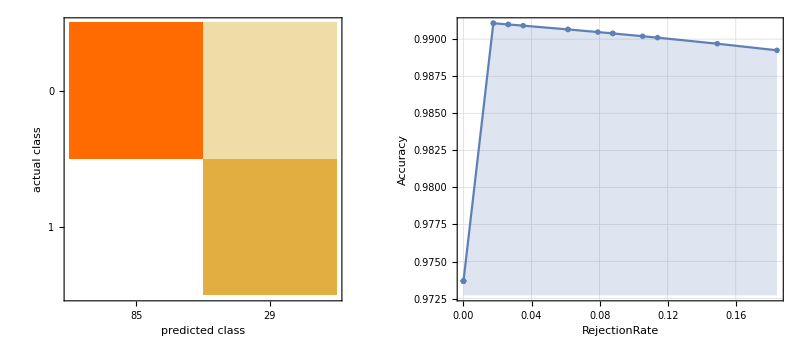

```mathematica
GraphicsRow[{cmSVM["ConfusionMatrixPlot"],cmSVM["AccuracyRejectionPlot"]}, Background->LightRed]
```

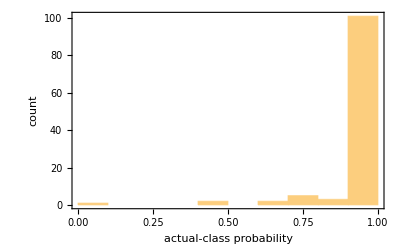

```mathematica
GraphicsRow[{cmSVM["ConfusionDistribution"], cmSVM["ProbabilityHistogram"]}, Background->LightBlue]
```

### Model Evaluations

```mathematica
Map[Info, algoSVM]
```

ClassifierFunction[…]

```mathematica
ModelInformation/@{algoSVM}
```

{Classifier information
Data type | Mixed (number: 30)
Classes | ,,01
Accuracy | (98.42.3) %
Method | SupportVectorMachine
Single evaluation time | 3.89 ms/example
Batch evaluation speed | 29.6 examples/ms
Loss | 0.0446 ± 0.024
Model memory | 353. kB
Training examples used | 455 examples
Training time | 2.72 s
 | }

## Neural Network Algorithm

### Fitting the model

```mathematica
Set[algoNN, Classify[trainFinal, Method->"NeuralNetwork", TargetDevice->"GPU"]]
```

ClassifierFunction[…]

### About the algorithm

```mathematica
ClassifierInformation[algoNN,"MethodDescription"]
```

An neural networks is composed of layers of artificial neuron units. Each 
unit computes its value as a function of the unit values in the previous layer. Information 
is processed layer by layer from the feature layer to the output layer which gives the class probabilities. It is 
also called a feed-forward neural network or a multi-layer perceptron.

### Evaluation Measurements

PROPERTIES : 
{Accuracy, AccuracyBaseline, AccuracyRejectionPlot, AreaUnderROCCurve, BatchEvaluationTime, BestClassifiedExamples, ClassifierFunction, ClassMeanCrossEntropy, ClassRejectionRate, CohenKappa, ConfusionDistribution, ConfusionFunction, ConfusionMatrix, ConfusionMatrixPlot, CorrectlyClassifiedExamples, DecisionUtilities, Error, EvaluationTime, Examples, F1Score, FalseDiscoveryRate, FalseNegativeExamples, FalseNegativeNumber, FalseNegativeRate, FalsePositiveExamples, FalsePositiveNumber, FalsePositiveRate, GeometricMeanProbability, IndeterminateExamples, LeastCertainExamples, Likelihood, LogLikelihood, MatthewsCorrelationCoefficient, MeanCrossEntropy, MeanDecisionUtility, MisclassifiedExamples, MostCertainExamples, NegativePredictiveValue, Perplexity, Precision, Probabilities, ProbabilityHistogram, Properties, Recall, RejectionRate, Report, ROCCurve, ScottPi, Specificity, TopConfusions, TrueNegativeExamples, TrueNegativeNumber, TruePositiveExamples, TruePositiveNumber, WorstClassifiedExamples}

```mathematica
cmNN=ClassifierMeasurements[algoNN,testFinal]
```

ClassifierMeasurementsObject[…]

```mathematica
(* cmNN/@{"Accuracy","FScore","Error",  "Precision"}//TableForm *)
```

```mathematica
PROPERTIES = {"Accuracy","EvaluationTime", "Error", "FScore",  "Precision", "Recall", "Specificity", "AreaUnderROCCurve"};
Do[Print[PROPERTIES[[i]], ": " ,cmNN[PROPERTIES[[i]]]], {i,  Length[PROPERTIES]}]
```

Accuracy: 0.982456

EvaluationTime: 0.0031

Error: 0.0175439

FScore: <|0→0.988506,1→0.962963|>

Precision: <|0→1.,1→0.928571|>

Recall: <|0→0.977273,1→1.|>

Specificity: <|0→1.,1→0.977273|>

AreaUnderROCCurve: <|0→0.999126,1→0.999126|>

### Confusion Matrix Plot and Accuracy vs Rejection Plot

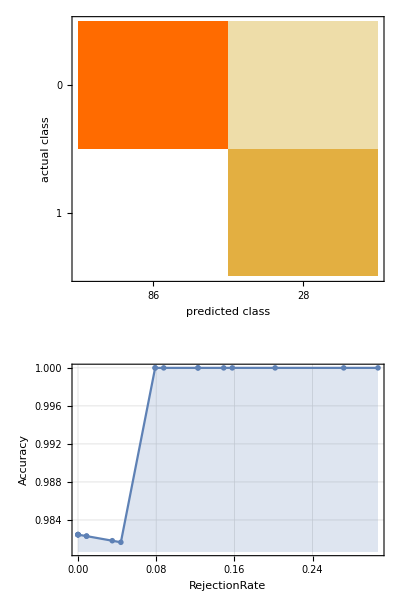

```mathematica
GraphicsColumn[{cmNN["ConfusionMatrixPlot"],cmNN["AccuracyRejectionPlot"]}, Background->Black]
```

```mathematica
cmNN["ConfusionDistribution"]
```

CategoricalDistribution[…]

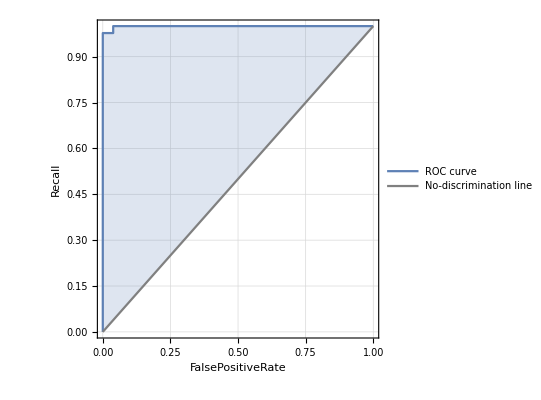
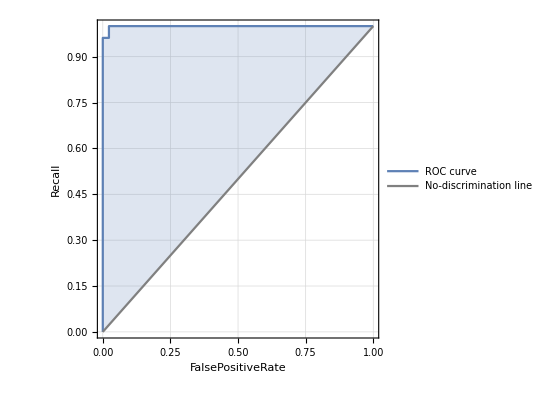
{<|0→-Graphics-,1→-Graphics-|>}

```mathematica
cmNN@{"ROCCurve"}
```

### Model Evaluations

```mathematica
Info/@algoNN
```

ClassifierFunction[…]

```mathematica
Map[ModelInformation[#]&, {algoNN}]
```

{Classifier information
Data type | Mixed (number: 30)
Classes | ,,01
Accuracy | (96.30.8) %
Method | NeuralNetwork
Single evaluation time | 2.27 ms/example
Batch evaluation speed | 45.4 examples/ms
Loss | 0.121 ± 0.019
Model memory | 835. kB
Training examples used | 455 examples
Training time | 1 21
 | }

## Evaluation

```mathematica
{{ALGORITHMS, ACCURACY, F-SCORE, ERROR, PRECISION}, {NaiveBayes, 0.8684, <|0->0.9534,1->0.8571|>, 0.0701, <|0->0.9761,1->0.8000|>}, {DecisionTree, 0.9298, <|0->0.9090,1->0.7619|>, 0.1315, <|0->0.9740,1->0.6486|>}, {RandomForest, 0.9649, <|0->0.9767,1->0.9285|>, 0.0350, <|0->1.000,1->0.8667|>}, {LogisticRegression, 0.9473, <|0->0.9659,1->0.8846|>, 0.0526, <|0->0.9659,1->0.8846|>}, {KNearestNeighbour, 0.9912, <|0->0.9943,1->0.9803|>, 0.0087, <|0->0.9887,1->1.0000|>}, {SupportVectorMachine, 0.9736, <|0->0.9826,1->0.9454|>, 0.0263, <|0->1.0000,1->0.8965|>}, {NeuralNetwork, 0.9473, <|0->0.9651,1->0.8928|>, 0.0526, <|0->0.9880,1->0.8334|>}} // TableForm;
```

## Fitting Models with Highly Correlated Features and Evaluation

## Highly correlated features

```mathematica
CorrelationFn[x_, y_]:=Correlation[train[All,x]//Normal, train[All,y]//Normal]
```

### Fetching Highly Correlated Features from the data

```mathematica
For[i =1, i≤ Length[header]-2, i++, 
	For[k =i+1, k≤Length[header]-1, k++, 
If[CorrelationFn[header[[i]], header[[k]]] > 0.85, Print["CORRELATION :: ",header[[i]], "-", header[[k]], "\n",CorrelationFn[header[[i]], header[[k]]]]]]]
```

CORRELATION :: radius_mean-perimeter_mean
0.997697

CORRELATION :: radius_mean-area_mean
0.988989

CORRELATION :: radius_mean-radius_worst
0.965381

CORRELATION :: radius_mean-perimeter_worst
0.961365

CORRELATION :: radius_mean-area_worst
0.939357

CORRELATION :: texture_mean-texture_worst
0.902807

CORRELATION :: perimeter_mean-area_mean
0.987604

CORRELATION :: perimeter_mean-radius_worst
0.965292

CORRELATION :: perimeter_mean-perimeter_worst
0.966843

CORRELATION :: perimeter_mean-area_worst
0.939192

CORRELATION :: area_mean-radius_worst
0.957439

CORRELATION :: area_mean-perimeter_worst
0.953573

CORRELATION :: area_mean-area_worst
0.952004

CORRELATION :: compactness_mean-concavity_mean
0.893376

CORRELATION :: compactness_mean-compactness_worst
0.86917

CORRELATION :: concavity_mean-concave points_mean
0.916922

CORRELATION :: concavity_mean-concavity_worst
0.883579

CORRELATION :: concavity_mean-concave points_worst
0.852318

CORRELATION :: concave points_mean-perimeter_worst
0.851339

CORRELATION :: concave points_mean-concave points_worst
0.906077

CORRELATION :: radius_se-perimeter_se
0.97009

CORRELATION :: radius_se-area_se
0.954597

CORRELATION :: perimeter_se-area_se
0.938311

CORRELATION :: radius_worst-perimeter_worst
0.993583

CORRELATION :: radius_worst-area_worst
0.986142

CORRELATION :: perimeter_worst-area_worst
0.978694

CORRELATION :: compactness_worst-concavity_worst
0.889038

CORRELATION :: concavity_worst-concave points_worst
0.857839

```mathematica
CorrelatedFeatures = {"radius_mean", "texture_mean", "perimeter_mean", "area_mean", "compactness_mean", "concavity_mean", "concave points_mean", "radius_se", "perimeter_se", "area_se", "radius_worst", "perimeter_worst", "area_worst", "compactness_worst","concavity_worst", "concave points_worst", "diagnosis"};
```

## Data Visualization

```mathematica
Needs["StatisticalPlots`"]
```

```mathematica
pairUp[x_,y_]:=({x[[#]],y[[#]]})&/@Range[Min[Length[x],Length[y]]];
```

### Pair Wise Scatter Plot

```mathematica
SlideView[{PairwiseScatterPlot[pairUp[train[All,"concave points_mean"],train[All,"radius_se"]],Background->Blue],PairwiseScatterPlot[pairUp[train[All,"concavity_mean"],train[All,"perimeter_se"]],Background->Red],PairwiseScatterPlot[pairUp[train[All,"compactness_mean"],train[All,"area_se"]],Background->Green],PairwiseScatterPlot[pairUp[train[All,"area_mean"],train[All,"radius_worst"]],Background->Orange],PairwiseScatterPlot[pairUp[train[All,"perimeter_mean"],train[All,"perimeter_worst"]],Background->LightBlue],PairwiseScatterPlot[pairUp[train[All,"texture_mean"],train[All,"area_worst"]],Background->Brown],PairwiseScatterPlot[pairUp[train[All,"radius_mean"],train[All,"compactness_worst"]],Background->Blue],PairwiseScatterPlot[pairUp[train[All,"concave points_worst"],train[All,"concavity_worst"]],Background->Red],PairwiseScatterPlot[pairUp[train[All,"concavity_worst"],train[All,"concave points_worst"]],Background->Green],PairwiseScatterPlot[pairUp[train[All,"compactness_worst"],train[All,"radius_mean"]],Background->Orange],PairwiseScatterPlot[pairUp[train[All,"area_worst"],train[All,"texture_mean"]],Background->LightBlue],PairwiseScatterPlot[pairUp[train[All,"perimeter_worst"],train[All,"perimeter_mean"]],Background->Brown],PairwiseScatterPlot[pairUp[train[All,"radius_worst"],train[All,"area_mean"]],Background->Blue],PairwiseScatterPlot[pairUp[train[All,"area_se"],train[All,"compactness_mean"]],Background->Red],PairwiseScatterPlot[pairUp[train[All,"perimeter_se"],train[All,"concavity_mean"]],Background->Green],PairwiseScatterPlot[pairUp[train[All,"radius_se"],train[All,"concave points_mean"]],Background->Orange]},ImageSize->Automatic,ImageMargins->11,Deployed->True,AppearanceElements->All]
```

## Fitting New Features into the Model

```mathematica
trainFeatures = train[1;;Length[train],CorrelatedFeatures];
testFeatures = test[1;;Length[test],CorrelatedFeatures];
```

## Flattening the Features

```mathematica
trainFinal=Flatten[Normal@trainFeatures[1;;Length[trainPrep],{Most@#->Last@#}&],1];
testFinal=Flatten[Normal@testFeatures[1;;Length[testPrep],{Most@#->Last@#}&],1];
```

## Building the Models and Evaluations

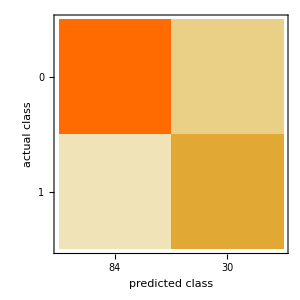
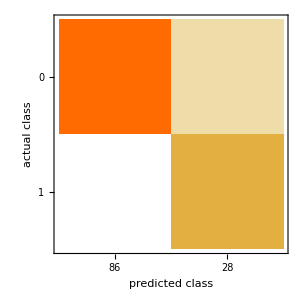
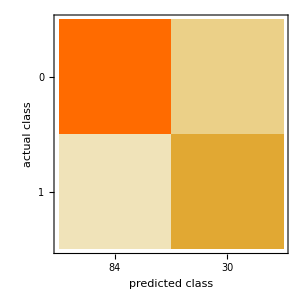
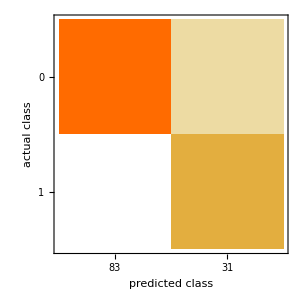
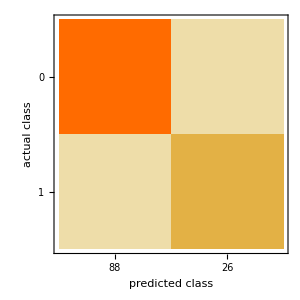
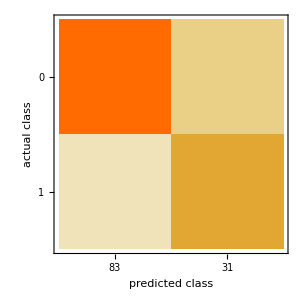
<|DecisionTree→{0.929825,0.00254,-Graphics-},RandomForest→{0.982456,0.004,-Graphics-},NaiveBayes→{0.947368,0.0043,-Graphics-},SupportVectorMachine→{0.95614,0.0041,-Graphics-},NearestNeighbors→{0.964912,0.0028,-Graphics-},LogisticRegression→{0.938596,0.0025,-Graphics-},NeuralNetwork→{0.938596,0.0028,-Graphics-}|>

```mathematica
AssociationMap[ClassifierMeasurements[Classify[trainFinal, Method->#],testFinal, {"Accuracy", "EvaluationTime", "ConfusionMatrixPlot"}]&,{"DecisionTree", "RandomForest","NaiveBayes","SupportVectorMachine","NearestNeighbors","LogisticRegression", "NeuralNetwork"}]
```

## Some Trained Neural Networks

## First Model

```mathematica
model1=NetInitialize@NetChain[{10,LogisticSigmoid,2,SoftmaxLayer[]},"Input"->{31},"Output"->NetDecoder[{"Class",{0,1}}]]
results1 = NetTrain[net,train,All,MaxTrainingRounds->1000]
trained1 = results["TrainedNet"];
```

### Trained Network

NetChain[<>]

NetTrain Results
summary | ,,  batches:7000  rounds:1000  time:5.4s  examples/s:83026
data | ,,  training examples:400  processed examples:448000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:8.32×10^-5  error:0%
 | 
 |

## Second Model

```mathematica
model2=NetChain[{LinearLayer[30],ElementwiseLayer[Ramp],LinearLayer[2],SoftmaxLayer[]},"Input"->{31},"Output"->NetDecoder[{"Class",{0, 1}}]]
results2 =  NetTrain[net,train,All,MaxTrainingRounds->1000]
```

NetChain[<>]

### Trained Network

NetTrain Results
summary | ,,  batches:7000  rounds:1000  time:5.3s  examples/s:84302
data | ,,  training examples:400  processed examples:448000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:5.92×10^-5  error:0%
 | 
 |

## Third Model

### Standardize Training and Testing Data

```mathematica
XtrainStandardized = Transpose@Map[Standardize, Transpose[traindata[[All, 1;;31]]]];
Mean[XtrainStandardized];// N
StandardDeviation[XtrainStandardized];// N
```

```mathematica
XtestStandardized = Transpose@Table[(testdata[[All, i]]-Mean[traindata[[All, 1;;31]]][[i]])/StandardDeviation[traindata[[All, 1;;31]]][[i]], {i, 31}];
Mean[XtestStandardized]; //N
StandardDeviation[XtestStandardized]; //N
```

### Sampling Training and Testing Data

```mathematica
XtrainN = 400;
```

```mathematica
trainT = Table[XtrainStandardized[[i, All]]->traindata[[All, 32]][[i]], {i, XtrainN}];
Dimensions[XtrainStandardized]
trainT[[;;1]]//N
```

{455,31}

{{-0.235825,1.07241,-2.10875,1.24768,0.969138,1.60098,3.2042,2.58485,2.47019,2.11866,2.29681,2.52737,-0.556382,2.87694,2.67297,-0.198597,1.24639,0.664473,0.631758,1.04287,0.861088,1.84685,-1.33608,2.27488,1.98188,1.28822,2.50837,2.04389,2.2167,2.57443,1.89354}→1.}

```mathematica
testT = Table[XtestStandardized[[i, All]]->testdata[[i]], {i, Length[testdata]}];
Dimensions[testT]
testT[[;;1]]//N
```

{114}

{{-0.161653,-0.244306,2.87318,-0.263811,-0.306928,-0.292917,-0.570627,-0.782561,-0.452191,-1.5938,-0.354458,-0.260925,1.35935,-0.31197,-0.284836,-0.385183,-0.716829,-0.766152,-0.449341,-0.608474,-0.297109,-0.289551,2.67826,-0.350785,-0.341876,-0.666813,-0.713425,-0.982979,-0.592132,-1.15505,-0.394348}→{9.11209×10^6,13.38,30.72,86.34,557.2,0.09245,0.07426,0.02819,0.03264,0.1375,0.06016,0.3408,1.924,2.287,28.93,0.005841,0.01246,0.007936,0.009128,0.01564,0.002985,15.05,41.61,96.69,705.6,0.1172,0.1421,0.07003,0.07763,0.2196,0.07675,0.}}

### Creating Network

#### Network Decoder

```mathematica
dr = NetDecoder[{"Class" , {0,1}}]
```

NetDecoder[<>]

#### Modelling

```mathematica
SeedRandom[123]
network= NetInitialize[NetChain[{5, Ramp, 2, SoftmaxLayer[]}, "Output"-> dr, "Input"-> 31], Method->{"Random", "Weights"->0.01, "Biases"->0}]
```

NetChain[<>]

#### Network Extraction

```mathematica
NetExtract[network, {1, "Weights"}]
```

NumericArray[…]

#### Network Analysis based on Weights and Bias using Histogram

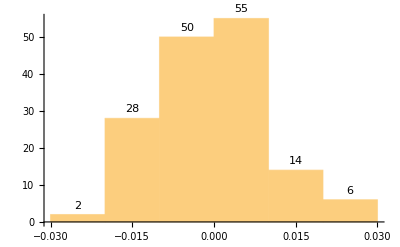

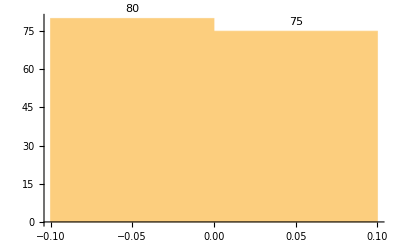

```mathematica
Histogram[Flatten[NetExtract[network, {1, "Weights"}]], {0.01}, ChartLegends->"Network Analysis with Weights 1 and Bias 0.01", LabelingFunction->Above]
Histogram[Flatten[NetExtract[network, {1, "Weights"}]], {0.1}, ChartLegends->"Network Analysis with Weights 1 and Bias 0.1", LabelingFunction->Above]
```

#### Trained Network

```mathematica
trained = NetTrain[network,train,All,MaxTrainingRounds->1000]
```

NetTrain Results
summary | ,,  batches:7000  rounds:1000  time:5.3s  examples/s:84245
data | ,,  training examples:400  processed examples:448000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.3×10^-3  error:0%
 | 
 |

## Conclusion

From the dataset used for breast cancer, without tuning the parameters and hyperparameters we observed that in initial model the best results has been shown by K-Nearest Neighbours with 99.12% and then by SVM algorithm with 97.36% while from the later model, fitting with highly correlated features have given maximum accuracy from Random Forest with 98.24%. Since, the model has obtained a reduce accuracy, it is clear that all the attributes are important to fit the model with higher accuracy (similar to the concept of R-Squared value where the this value always increases on adding more features to the data). 

For the point of improvement, hyperparameters can be tuned with similar model, increasing the hidden layer and dynamics of the neural network can also result will give more profound result as we obtained while training the network with 3 optimized (i.e., over hidden layers, activation function, weights , bias and methods ) models at the last. Moreover, Image classification can be more accurate and effective in case of Breast Cancer Classification, when integrated with the Data Resampling, Data Augmentation, Transfer Learning and building hybrid models.

## References

[1]. Myers ER, Moorman P, Gierisch JM, et al. Benefits and harms of breast cancer screening: a systematic review. JAMA. 2015;314:1615–1634. [PubMed] [Google Scholar]
[2]. Group DES. Systematic review of cancer screening literature for updating American Cancer Society breast cancer screening guidelines. Duke Clinical Research Institute, Durham, NC: Guidelines Development Group. 2014 [Google Scholar]
[3]. Swedish Council on Health Technology Assessment. Computer-Aided Detection (CAD) in mammography screening. Stockholm: 2011. SBU systematic review summaries. [Google Scholar]
[4]. Mehdi Habibzadeh Motlagh, Mahboobeh Jannesari, HamidReza Aboulkheyr, Pegah Khosravi, Olivier Elemento, Mehdi Totonchi, and Iman Hajirasouliha
[5]. Babak Ehteshami Bejnordi, Guido Zuidhof, Maschenka Balkenhol, Meyke Hermsen, Peter Bult, Bram van Ginneken, Nico Karssemeijer, Geert Litjens, Jeroen van der Laak 
[6]. Alexander Rakhlin, Alexey Shvets, Vladimir Iglovikov and Alexandr A. Kalinin
[7]. Nan Wu, Jason Phang, Jungkyu Park, Yiqiu Shen, Zhe Huang, Masha Zorin, Stanisław Jastrz˛ebsk, Thibault Févrb, Joe Katsnelson, Eric Kim, Stacey Wolfson, Ujas Parikha, Sushma Gaddama, Leng Leng Young Lina, Kara Hoj* , Joshua D. Weinsteina, Beatriu Reig, Yiming Gao, Hildegard Totha, Kristine Pysarenkoa, Alana Lewina, Jiyon Leea, Krystal Airolaa, Eralda Memaa, Stephanie Chung, Esther Hwang, Naziya Samreena, S. Gene Kima, , Laura Heacocka, Linda Moya, Kyunghyun Chob, and Krzysztof J. Gerasa
[8]. Krzysztof J. Geras, Stacey Wolfson, Yiqiu Shen, Nan Wu, S. Gene Kim, Eric Kim, Laura Heacock, Ujas Parikh, Linda Moy, Kyunghyun Cho
[9]. Quinlan JR, Rivest RL. Inferring decision trees using the minimum description length principle. Information and Computation. 1989 March 1;80(3):227–48.
[10]. Quinlan JR. Simplifying decision trees. International Journal of Man-Machine Studies. 1987 September 1;27(3):221–34.
[11]. Mehta M, Rissanen J, Agrawal R. MDL-based decision tree pruning. KDD. 1995 August 20;21(2):216–221.
[12]. Xindong Wu, Vipin Kumar, J. Ross Quinlan, Joydeep Ghosh, Qiang Yang, Hiroshi Motoda, Geoffrey J. McLachlan, Angus Ng, Bing Liu and Philip S. Yu, et al., “Top 10 algorithms in data mining”, Knowledge and Information Systems, Vol. 14, No. 1, 1-37, DOI: 10.1007/s10115-007- 0114-2. 
[13]. Hang Yang, Fong, S, “Optimized very fast decision tree with balanced classification accuracy and compact tree size,” Data Mining and Intelligent Information Technology Applications (ICMiA), 2011 3rd International Conference on, Pp.57-64, 24-26 Oct. 2011.
[14]. Kamiński, B.; Jakubczyk, M.; Szufel, P. (2017). “A framework for sensitivity analysis of decision trees”. Central European Journal of Operations Research. 26 (1): 135–159. doi:10.1007/s10100-017-0479-6. PMC 5767274. PMID 29375266.
[15]. ^ Quinlan, J. R. (1987). “Simplifying decision trees”. International Journal of Man-Machine Studies. 27 (3): 221–234. CiteSeerX 10.1.1.18.4267. doi:10.1016/S0020-7373(87)80053-6.
[16]. Ho, Tin Kam (1995). Random Decision Forests (PDF). Proceedings of the 3rd International Conference on Document Analysis and Recognition, Montreal, QC, 14–16 August 1995. pp. 278–282. Archived from the original (PDF) on 17 April 2016. Retrieved 5 June 2016.
[17]. ^ Jump up to:a b c d Ho TK (1998). “The Random Subspace Method for Constructing Decision Forests” (PDF). IEEE Transactions on Pattern Analysis and Machine Intelligence. 20 (8): 832–844. doi:10.1109/34.709601.

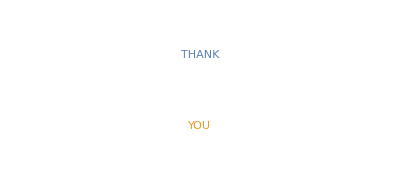

```mathematica
WordCloud[{"THANK","YOU"},PreprocessingRules->s_String:>First[SpellingCorrectionList[s]]]
```